# Verifying the variable step size and continuous time variants of the within-host pathogen processes.

## Appendix to “Integrating infection intensity into within- and between-host parasite dynamics: implications for invasion and virulence evolution” by Wilber et al 2021

## This notebook demonstrates 1. how the within-host dynamics of the Log parasite load can be generalized for variable time steps based on a Ohrnstein-Uhlenbeck process, and 2. how a continuous time Fokker-Planck equation can be used to compute the probability density function of the Log parasite load at any time. The different approaches are compared, demonstrating that they describe the same process. To keep the demonstration simple, we assume there is no mortality and no loss of infection.

### Part 1: Stochastic Ohrnstein-Uhlenbeck process. The trajectory of the Log parasite load of an individual in the full IPM is described by a stochastic Ohrnstein-Uhlenbeck process. Here we verify the equations stated in the Appendix for changing the step size in the discrete time model.

Defining the model and setting up simulations

```mathematica
(*function to draw normal distributed random variable with mean μ and standard deviation σ*)
c[μ_,σ_]:=RandomVariate[NormalDistribution[μ,σ]];
(*parameter values*)
(*Log pathogen growth rate*)
a=.7;
(*Density-dependence of within-host pathogen growth*)
b=.8;
(*standard deviation of pathogen growth function*)
σ=.3;
(*initial Log pathogen load*)
x0=0;
(*time to simulate*)
tmax=10;
(*function to simulate one run, x=Log pathogen load*)
dat[a_,b_,σ_,x0_,Δt_]:=
Module[{x,τmax=tmax/Δt},
x[0]=x0;
(*here is the next time step equation for the pathogen load*)
x[τ_]:=x[τ]=c[a/(1-b)(1-b^Δt)+b^Δt x[τ-1],√(σ^2/(1-b^2)(1-b^(2Δt)))];
Table[{Δt τ,x[τ]},{τ,0,τmax}]
];
(*time step values Δt for tests*)
Δts={1,.01};
```

#### Some model runs for the Log parasite load x with different step sizes Δt. Using a smaller Δt adds more steps, but does not change the behavior of the model one the bigger time scale.

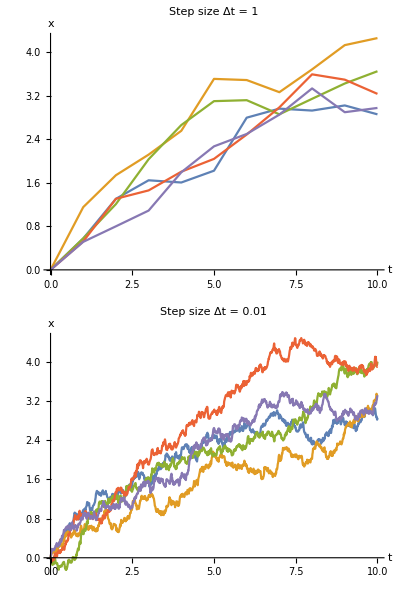

```mathematica
Column[Table[ListPlot[Table[dat[a,b,σ,x0,Δt],5],AxesLabel->{"t","x"},Joined->True,PlotRange->Full,PlotLabel->Row[{"Step size Δt = ",Δt}]],{Δt,Δts}]]
```

Simulating many model runs to compare the outcomes qualitatively.

```mathematica
(*histogram of final values at tmax*)
(*number of runs*)
totalruns=10000;
(*run model repeatedly, save final values*)
discretetests=Table[{Δt,Table[dat[a,b,σ,x0,Δt],totalruns][[All,-1,2]]},{Δt,{.01,1}}];
```

#### Draw histograms of simulated probability density functions at final time step (how often simulations ended up in the given x-ranges), and calculate the final mean and variance of x. The simulations verify that the final probability density function is independent of the step size Δt.

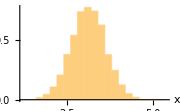
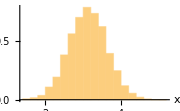
Step size Δt = 0.01
-Graphics-Mean  | 3.12092
Variance  | 0.252901
Step size Δt = 1
-Graphics-Mean  | 3.12404
Variance  | 0.25249

```mathematica
Column[Column[{Row[{"Step size Δt = ", #[[1]]}],Row[{Histogram[#[[2]],{.2},"PDF",AxesLabel->{"x"},ImageSize->Small],Grid[{{"Mean ",Mean[#[[2]]]},{"Variance ",Variance[#[[2]]]}},Alignment->Left]}]},Alignment->Center]&/@discretetests]
```

#### Part 2: Fokker-Planck representation. Here we test the equations stated in the Appendix for translating the within-host pathogen dynamics to continuous time.

Defining and simulating the model.

```mathematica
(*parameters for partial differential equation (PDE)*)
θ=-Log[b];
μ=a/(1-b);
d=-σ^2 Log[b]/(1-b^2);
(*simulation*)
(*mininmal and maximal x values for simulation*)
xmin=-1;xmax=5;
(*initial variance for simulation (very small, effectively starting at single point)*)
σini=.001;
(*initial distribution of Log pathogen load*)
u0[x_]:=PDF[NormalDistribution[x0,σini],x];
(*solve PDE numerically*)
sol=NDSolve[{
(*here is the Fokker-Planck equation*)
D[u[t,x], t]==-θ D[((μ-x)u[t,x]), x]+d D[u[t,x], x,x],
u[0,x]==u0[x],
u[t,xmin]==u0[xmin],
u[t,xmax]==u0[xmax]
},u,{t,0,tmax},{x,xmin,xmax},
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->10^6,"MinPoints"->10^3}}];
```

#### Solution of Fokker-Planck equation: probability density function of Log parasite load x over time.

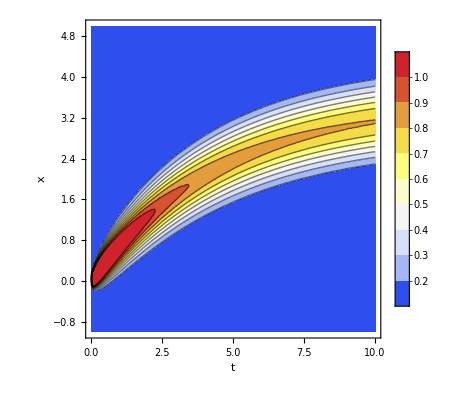

```mathematica
ContourPlot[u[t,x]/.sol,{t,0,tmax},{x,xmin,xmax},FrameLabel->{"t","x"},PlotLegends->Automatic,Contours->Range[.2,1,.1],PlotRange->All,
ColorFunction->(ColorData["TemperatureMap",Rescale[#,{0,1}]]&),ColorFunctionScaling->False]
```

#### Fokker-Planck solution: probability density function, mean, and variance of x at final time.

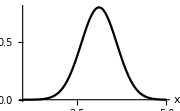
-Graphics-Mean | 3.12234
Variance | 0.246011

```mathematica
Row[{Plot[u[tmax,x]/.sol,{x,1,xmax},PlotStyle->Black,AxesLabel->{"x"},ImageSize->Small],
Grid[{{"Mean",
meanu=NIntegrate[x u[tmax,x]/.sol,{x,xmin,xmax}][[1]]},
{"Variance",
varu=NIntegrate[u[tmax,x](meanu-x)^2/.sol,{x,xmin,xmax}][[1]]}},Alignment->Left]}]
```

### Compare stochastic Ohrnstein-Uhlenbeck processes and Fokker-Planck solution.

#### Mean and variance of Log parasite load at final time.

```mathematica
Grid[Join[{{"","Mean","Variance"}},{{"Fokker-Planck solution",meanu,varu}},{Row[{"Stochastic Ohrnstein-Uhlenbeck simulations with step size Δt=",#[[1]]}],Mean[#[[2]]],Variance[#[[2]]]}&/@discretetests],Alignment->Left]
```

| Mean | Variance
Fokker-Planck solution | 3.12234 | 0.246011
Stochastic Ohrnstein-Uhlenbeck simulations with step size Δt=0.01 | 3.12092 | 0.252901
Stochastic Ohrnstein-Uhlenbeck simulations with step size Δt=1 | 3.12404 | 0.25249

#### Histograms of Log parasite load at final time.

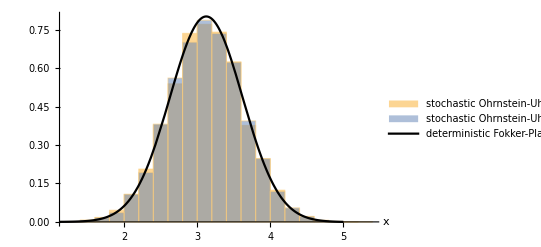

```mathematica
Show[Histogram[discretetests[[All,2]],Automatic,"PDF",ChartLegends->(Row[{"stochastic Ohrnstein-Uhlenbeck process, Δt = ",#}]&/@discretetests[[All,1]]),AxesLabel->{"x"}],Plot[u[tmax,x]/.sol,{x,xmin,xmax},PlotStyle->Black,PlotLegends->{"deterministic Fokker-Planck equation"}]]
```